```mathematica
datano=Import["/home/sander/Downloads/novacbea.dat"];
datavac=Import["/home/sander/Downloads/vacbea.dat"];
```

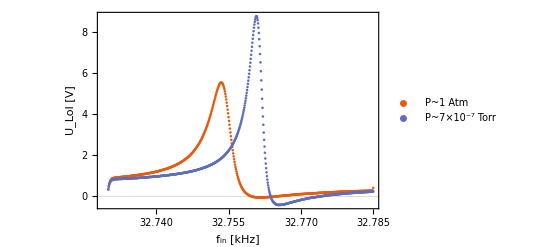

```mathematica
ListPlot[{datano,datavac},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"f_in [kHz]","U_LoI [V]"},PlotLegends->{"P~1 Atm","P~7×10^-7 Torr"}]
```

```mathematica
f0=32.75;
```

General::munfl: Exp[-763.058] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6224.01] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
α | 0.0000144987 | 1.66043×10^-7 | 87.319 | 0.
c | 1441.34 | 30.0352 | 47.9884 | 2.37308×10^-202
q | 2.48156×10^-6 | 4.52587×10^-8 | 54.8304 | 1.79646×10^-229
ω0 | 32.7534 | 0.000024987 | 1.31082×10^6 | 0.

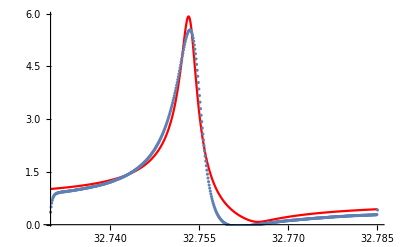

```mathematica
fno=NonlinearModelFit[datano,{α(ω)(((1+ c(1-(ω/ω0)^2))^2+c^2(ω q)^2)/((1-(ω/ω0)^2)^2+(ω q)^2))^(1/2)},{{α,0.0005},{c,1500},{q,2*^-6},{ω0,f0}},ω];
Print[fno["ParameterTable"]];
Show[Plot[fno[x],{x,32.73,32.785},PlotStyle->Red,PlotRange->Full],ListPlot[datano]]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: Exp[-7192.64] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
α | 0.0000132183 | 2.1722×10^-7 | 60.852 | 1.32458×10^-270
c | 1836. | 56.1612 | 32.6917 | 2.24456×10^-139
q | 1.39883×10^-6 | 3.69461×10^-8 | 37.8613 | 1.46845×10^-166
ω0 | 32.7606 | 0.0000202061 | 1.62132×10^6 | 0.

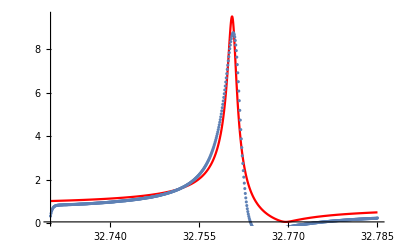

```mathematica
fvac=NonlinearModelFit[datavac,{α(ω)(((1+ c(1-(ω/ω0)^2))^2+c^2(ω q)^2)/((1-(ω/ω0)^2)^2+(ω q)^2))^(1/2)},{{α,0.0005},{c,1500},{q,2*^-6},{ω0,f0}},ω];
Print[fvac["ParameterTable"]];
Show[Plot[fvac[x],{x,32.73,32.785},PlotStyle->Red,PlotRange->Full],ListPlot[datavac]]
```

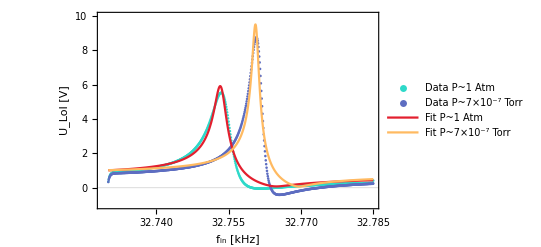

```mathematica
Show[ListPlot[{datano,datavac},PlotRange->{Automatic,{-1,10}},PlotTheme->"Scientific",FrameLabel->{"f_in [kHz]","U_LoI [V]"},PlotLegends->{"Data P~1 Atm","Data P~7×10^-7 Torr"},PlotStyle->{RGBColor[0.18,0.85,0.79],Automatic}],Plot[{fno[f],fvac[f]},{f,32.73,32.785},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"f_in [kHz]","U_LoI [V]"},PlotLegends->{"Fit P~1 Atm","Fit P~7×10^-7 Torr"},PlotStyle->{{Thickness->.002,RGBColor[0.89,0.12,0.18]},{Thickness->.002,RGBColor[1.,0.73,0.38]}}]]
```

```mathematica
fno2=NonlinearModelFit[datano,{(i*ω/q*ω0)(((1+ c(1-(ω/ω0)^2))^2+c^2(ω q)^2)/((1-(ω/ω0)^2)^2+(ω q)^2))^(1/2)},{{i,0.0005},{c,1500},{q,2*^-6},{ω0,f0}},ω];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
Print[fno2["ParameterTable"]];
Show[Plot[fno2[x],{x,32.73,32.785},PlotStyle->Red,PlotRange->Full],ListPlot[datano]]
```

General::munfl: Exp[-16979.6] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-6264.11] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
i | 1.09849×10^-12 | 2.70337×10^-14 | 40.6341 | 1.73208×10^-170
c | 1441.34 | 7.01961×10^-12 | 2.05331×10^14 | 0.
q | 2.48156×10^-6 | 4.11017×10^-8 | 60.3761 | 8.02327×10^-250
ω0 | 32.7534 | 0.0000232893 | 1.40637×10^6 | 0.

-Graphics-

```mathematica
fvac2=NonlinearModelFit[datavac,{(i*ω/q*ω0)(((1+ c(1-(ω/ω0)^2))^2+c^2(ω q)^2)/((1-(ω/ω0)^2)^2+(ω q)^2))^(1/2)},{{i,0.0005},{c,1500},{q,2*^-6},{ω0,f0}},ω];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::munfl: Exp[-20306.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-7219.36] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
i | 5.64398×10^-13 | 1.95321×10^-14 | 28.8959 | 1.01845×10^-118
c | 1836. | 1.96016×10^-12 | 9.36659×10^14 | 0.
q | 1.39883×10^-6 | 3.27909×10^-8 | 42.659 | 1.39282×10^-190
ω0 | 32.7606 | 0.0000193923 | 1.68937×10^6 | 0.

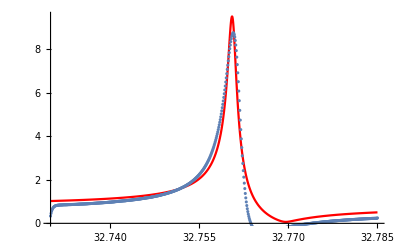

```mathematica
Print[fvac2["ParameterTable"]];
Show[Plot[fvac2[x],{x,32.73,32.785},PlotStyle->Red,PlotRange->Full],ListPlot[datavac]]
```

```mathematica
Show[ListPlot[{datano,datavac},PlotRange->{Automatic,{-1,10}},PlotTheme->"Scientific",FrameLabel->{"f_in [kHz]","U_LoI [V]"},PlotLegends->{"Data P~1 Atm","Data P~7×10^-7 Torr"},PlotStyle->{RGBColor[0.18,0.85,0.79],Automatic}],Plot[{fno2[f],fvac2[f]},{f,32.73,32.785},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"f_in [kHz]","U_LoI [V]"},PlotLegends->{"Fit P~1 Atm","Fit P~7×10^-7 Torr"},PlotStyle->{{Thickness->.002,RGBColor[0.89,0.12,0.18]},{Thickness->.002,RGBColor[1.,0.73,0.38]}}]]
```

-Graphics-